```mathematica
ClearAll["Global`*"]
```

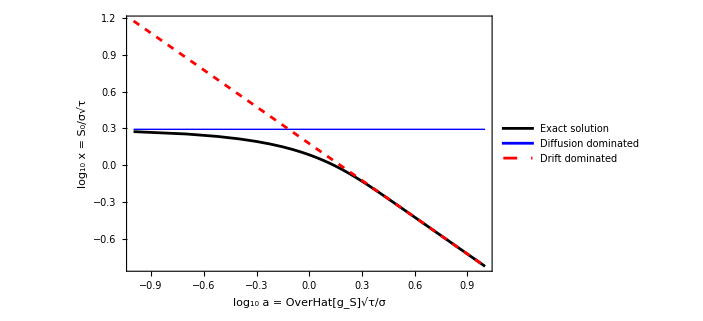

```mathematica
(*Basic constants*)
ε=0.05;                             (*acceptable ruin probability*)
φ=InverseCDF[NormalDistribution[],1-ε/2];   (* ≈1.95996*)

(*Full ruin equation f(x|a)*)

Clear[f]
CDFN[z_]:=CDF[NormalDistribution[],z];
f[x_,a_]:=Exp[-2 a x] CDFN[-(x-a)]+CDFN[-(x+a)]-ε;

(*Exact root SExact(a) with adaptive starting guess*)

SExact[a_?NumericQ]:=
Module[{xSeed,sol},xSeed=If[
a<φ,φ,(*diffusion seed*)
Log[1/ε]/(2 a)          (*drift seed*)
];
sol=Quiet@FindRoot[
f[x,a]==0,{x,xSeed},WorkingPrecision->30,AccuracyGoal->15,PrecisionGoal->15
];
If[
MatchQ[sol,{_->_}],x/. sol,Missing["noRoot"]
]
]

(*Two asymptotic formulas (σ √τ normalised to 1)*)
Sdiff[a_]:=φ;                       (*diffusion approximation*)
Sdrift[a_]:=Log[1/ε]/(2 a);          (*drift approximation*)

(* ::Section::*)
(*Evaluate over a grid of a-values*)

aVals=Range[0.1,10,0.1];
exact=Table[{Log10[a],Log10[SExact[a]]},{a,aVals}];
diffApp=Table[{Log10[a],Log10[Sdiff[a]]},{a,aVals}];
driftApp=Table[{Log10[a],Log10[Sdrift[a]]},{a,aVals}];

(*Remove any points where FindRoot failed*)
exact=DeleteCases[exact,{_,_Missing}];

(*Plot*)
diffdriftplot = ListLinePlot[
{exact,(*black–exact root*)
diffApp,(*blue–diffusion approx*)
driftApp       (*red–drift approx*)
},PlotStyle->{Black,{Blue,Thick},{Red,Dashed}},PlotLegends->Placed[{"Exact solution","Diffusion dominated","Drift dominated"},{Scaled[{0.01,0.25}], {0, 0.7}}],Frame->True,FrameLabel->{"log_10 a = OverHat[g_S]√τ/σ","log_10 x = S_0/σ√τ"},LabelStyle->Directive[Black,FontSize->16],ImageSize->520]
```

```mathematica
namespace = StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2025_fatscaling"}]
Export[StringJoin[namespace,"/figures/fig_diffdrift.pdf"],diffdriftplot]
```

/Users/jdyeakel/Dropbox/PostDoc/2025_fatscaling

/Users/jdyeakel/Dropbox/PostDoc/2025_fatscaling/figures/fig_diffdrift.pdf